```mathematica
pdf={{"-",120332},{"0",24320},{"1",32426},{"2",29841},{"3",19390},{"4",18611},{"5",13899},{"6",12393},{"7",11609},{"8",15448},{"9",12737},{"_",255},{"A",930794},{"B",245537},{"C",373911},{"D",327954},{"E",1006366},{"F",169800},{"G",248782},{"H",258077},{"I",746503},{"J",56986},{"K",188342},{"L",477495},{"M",338951},{"N",618224},{"O",738512},{"P",282326},{"Q",20848},{"R",648487},{"S",667752},{"T",624012},{"U",335063},{"V",132085},{"W",130378},{"X",66844},{"Y",182189},{"Z",70884}};
pdf=SortBy[Map[{ToCharacterCode[Characters[#[[1]]][[1]]][[1]],(#[[2]])/Total[Transpose[pdf][[2]]]}&,pdf],#[[1]]&]//N;
Entropy[pdf[[All,2]]]//N
Times@@Transpose[pdf]//Total
Mean[pdf[[All,1]]]
(%%)/%
```

3.63759

74.8797

70.5263

1.06173

```mathematica
UniformSample=Function[{list,num},
If[num≥Length[list],
list,
list[[1;;;;Floor[Length[list]/num]]]
]
];
```

```mathematica
RandomSubsets=Function[{list,length,max},
If[Length[list]^length≤max,
Tuples[Table[list,{length}]],
Table[
RandomChoice[list,length],{max}]
]
];
RandomSubsetsC=Compile[{{list,_Real,2},{length,_Integer},{max,_Integer}},RandomSubsets[list,length,max]];
```

```mathematica
Observations=Function[{list,n,max},
Module[{possibilities={{0.0},{0.0}},t=0.0},
possibilities=SortBy[
Map[
{Norm[#[[1]]],Times@@#[[2]]}&[Transpose[#]]&
,
RandomSubsets[list,n,max]
]
,
#[[1]]&];
t=Total[possibilities[[All,2]]];
Map[{#[[1]],(#[[2]])/t}&,possibilities]
]
];
```

```mathematica
ObservationsL=Function[{list,n,max},
Module[{t={{0.0},{0.0}},pt=0.0},
t=Table[
{Norm[#[[1]]],Times@@#[[2]]}&[Transpose[RandomChoice[list,n]]],
{max}
];
pt=t[[All,2]]//Total;
Map[{#[[1]],(#[[2]])/pt}&,t]
]
];
ObservationsLC=Compile[{{list,_Real,2},{n,_Integer},{max,_Integer}},ObservationsL[list,n,max],RuntimeOptions->"Speed"];
```

```mathematica
ListInterpolation2D=Function[{l},
Module[{lix,liy},
{lix,liy}=Map[ListInterpolation[#,{{0,1}}]&,Transpose[l]];
Function[{t},
liy[lix[t]]
]
]
];
```

```mathematica
cv=ParallelTable[Observations[pdf,i,100000],{i,1,100}];//AbsoluteTiming
```

{19.69313,Null}

```mathematica
cv2=ParallelTable[ObservationsL[pdf,i,100000],{i,1,100}];//AbsoluteTiming
```

{12.73173,Null}

```mathematica
cv3=ParallelTable[ObservationsLC[pdf,i,100000],{i,1,100}];//AbsoluteTiming
```

{12.81673,Null}

```mathematica
ev=Map[
Total[Times@@Transpose[#]]&,
cv3];//AbsoluteTiming
av=Map[Mean,cv3][[All,1]];//AbsoluteTiming
```

{0.57503,Null}

{0.20201,Null}

```mathematica
Show[Plot[{Fit[ev,{1,√y},y]/.y->x,Fit[av,{1,√y},y]/.y->x},{x,0,Length[ev]},PlotStyle->Thick],ListPlot[{ev,av},PlotStyle->PointSize[0.01],PlotLegends->LineLegend[{"Expected Value","Mean Value"}]],ImageSize->500,PlotLabel->"Growth of Expected and Mean\nNorms of Sampled Vectors",AxesLabel->{"Dimension of\nSampled Vectors","Norm"}]
```

$Aborted

(-0.148363+75.3486 √x)/(-1.19795+72.1096 √x)

1.04492

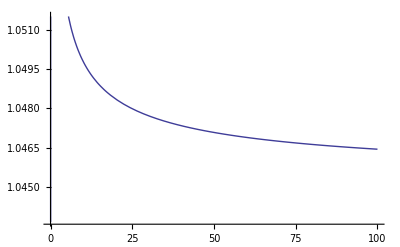

```mathematica
(Fit[ev,{1,√y},y]/.y->x)/(Fit[av,{1,√y},y]/.y->x)
Limit[(Fit[ev,{1,√y},y]/.y->x)/(Fit[av,{1,√y},y]/.y->x),x->∞]
Plot[(Fit[ev,{1,√y},y]/.y->x)/(Fit[av,{1,√y},y]/.y->x),{x,0,100}]
```

```mathematica
acv=Map[Transpose[{(#[[All,1]])/(#[[All,1]]//Max),#[[All,2]]//Accumulate}]&,cv];//AbsoluteTiming
```

{0.79905,Null}

```mathematica
fits=(1+Erf[a x+b])/2/.ParallelMap[FindFit[#,(1+Erf[a x+b])/2,{a,b},x]&,acv[[1;;20]]];//AbsoluteTiming
```

{5.01829,Null}

```mathematica
Manipulate[
Show[
ListPlot[
RandomSample[acv[[i]],Min[Length[acv[[i]]],1000]],PlotRange->{{0,1},{0,1}}
],
Plot[fits[[i]],{x,0,1}]
]
,{i,1,Length[fits],1}]
```

```mathematica
Plot[fits,{x,0,1},PlotStyle->Table[Hue[(0.75i)/Length[cv]],{i,0,Length[cv]-1}]]
```

General::unfl: Underflow occurred in computation.

```mathematica
mse=ParallelTable[Total[Map[(#[[2]]-fits[[i]]/.x->#[[1]])^2&,acv[[i]]]]/Length[acv[[i]]],{i,1,30}]
```

{0.000882132,0.266865,0.0000721062,0.0000514205,0.0000418599,0.000073488,0.0000473239,0.000294447,0.00017937,0.000272392,0.000210766,0.000472843,0.000342835,0.106235,0.06218,0.00310163,0.0185776,0.0955376,0.106496,0.0955109,0.0285089,0.109545,0.0629573,0.0998997,0.0367808,0.0505655,0.0555842,0.114376,0.129405,0.144366}

```mathematica
msre=ParallelTable[Total[Map[((#[[2]]-fits[[i]]/.x->#[[1]])/(#[[2]]))^2&,acv[[i]]]]/Length[acv[[i]]],{i,1,30}]
```

{0.185103,1.,0.133723,0.114131,0.136141,0.154982,0.13864,0.0654411,0.182233,0.266196,0.260151,0.466853,0.14889,1.,1.,0.489388,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
k=5;
ListPlot[
acv[[1;;k]],Joined->True,PlotRange->{{0,1},{0,1}},PlotStyle->Map[{Thick,Darker[#]}&,Table[Hue[i/k],{i,0,k-1}]]]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
Plot[fits[[1;;k]],{x,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Map[{Dashed,Thick,Darker[#]}&,Table[Hue[i/k],{i,0,k-1}]]]
```

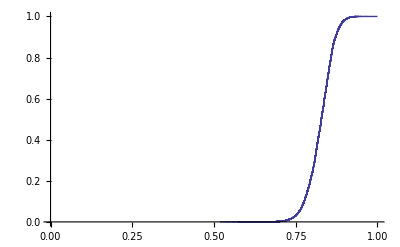

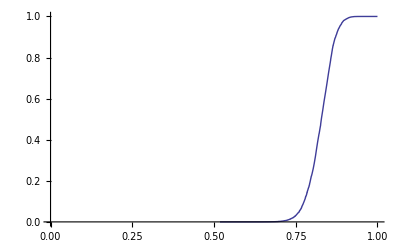

```mathematica
t=Map[Transpose[{(#[[All,1]])/(#[[All,1]]//Max),#[[All,2]]//Accumulate}]&,{cv[[5]]}][[1]];
ListPlot[t,Joined->True,AxesOrigin->{0,0}]
(*ListPlot[{Transpose[{t[[All,1]][[;;-2]],MeanFilter[Differences[t[[All,2]]],1000]}]},Joined->True,PlotRange->All]*)
lix=ListInterpolation[t[[All,1]],{{0,1}}];
liy=ListInterpolation[t[[All,2]],{{0,1}}];
ParametricPlot[{lix[u],liy[u]},{u,0,1},AxesOrigin->{0,0},AspectRatio->1/GoldenRatio]
```

## Testing Hypothesis : Convolution is for IID Observations = NOPE

ConditionalExpression[-√2 InverseErfc[2 p],0≤p≤1]

1/2 (1+Erf[p/2])

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2 InverseErf[-1+2 #1]&

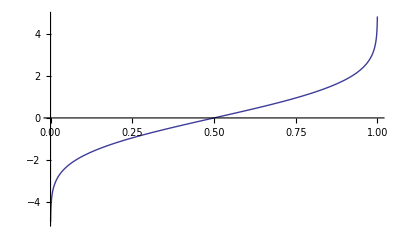

```mathematica
InverseCDF[NormalDistribution[0,1],p]
Integrate[(ⅇ^(-x^2/4))/(2 √π),{x,-∞,p}]
InverseFunction[1/2 (1+Erf[#/2])&]
Plot[2 InverseErf[-1+2 p],{p,0,1}]
```

(ⅇ^(-x^2/4))/(2 √π)

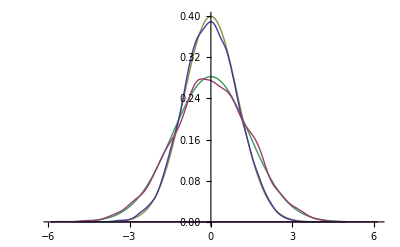

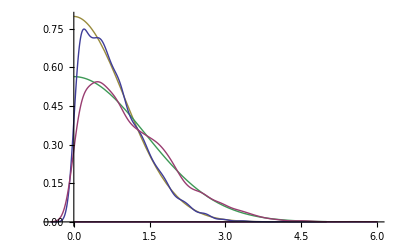

```mathematica
Convolve[PDF[NormalDistribution[0,1],y],PDF[NormalDistribution[0,1],y],y,x]
pts1=-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{5000}];
pts2=2 InverseErf[-1+2 x]/.x->Table[RandomReal[{0,1}],{5000}];
Show[Plot[{0,0,PDF[NormalDistribution[0,1],x],(ⅇ^(-x^2/4))/(2 √π)},{x,-5,5},PlotRange->All],SmoothHistogram[{pts1,pts2}]]
Show[Plot[{0,0,2PDF[NormalDistribution[0,1],x],2(ⅇ^(-x^2/4))/(2 √π)},{x,0,5},PlotRange->All],SmoothHistogram[{Abs[pts1],Abs[pts2]}]]
```

```mathematica
Plot3D[PDF[NormalDistribution[0,1],x]PDF[NormalDistribution[0,1],y],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->50]
```

-Graphics3D-

-Graphics3D-

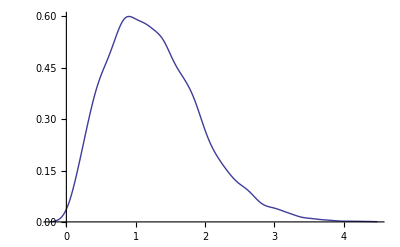

```mathematica
pts3={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{5000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{5000}]}//Transpose;
SmoothHistogram3D[pts3]
SmoothHistogram[Map[Norm,pts3]]
```

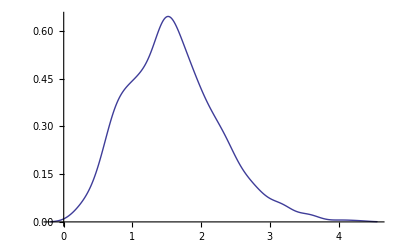

```mathematica
pts4={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}]}//Transpose;
SmoothHistogram[Map[Norm,pts4]]
```

```mathematica
pts5={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}]}//Transpose;
```

```mathematica
pts6={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}]}//Transpose;
```

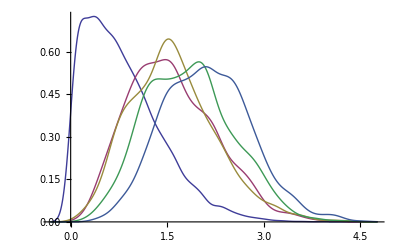

```mathematica
SmoothHistogram[{Abs[pts1],Map[Norm,pts3],Map[Norm,pts4],Map[Norm,pts5],Map[Norm,pts6]}]
```

```mathematica
s={a,b,c,d,e,f,g,h}
Total[s]^2//Expand
```

{a,b,c,d,e,f,g,h}

a^2+2 a b+b^2+2 a c+2 b c+c^2+2 a d+2 b d+2 c d+d^2+2 a e+2 b e+2 c e+2 d e+e^2+2 a f+2 b f+2 c f+2 d f+2 e f+f^2+2 a g+2 b g+2 c g+2 d g+2 e g+2 f g+g^2+2 a h+2 b h+2 c h+2 d h+2 e h+2 f h+2 g h+h^2